```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Estimator Parameters: Length of Wilson Lines:*)
L:=10
(*Number of Time Steps:*)
n:=10
(*Distance between instanton and anti-instanton*)
R:=5
(*Distance between quark and anti-quark*)
r:=1
(*Integration Bounds*)
l:=3
```

```mathematica
η:=Array[Eta,{4,4,3}]
Do[Eta[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Eta[4,4,a]=0,{a,1,3}]
Do[Eta[k,4,a]=KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Eta[4,k,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
ηbar:=Array[Etabar,{4,4,3}]
Do[Etabar[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Etabar[4,4,a]=0,{a,1,3}]
Do[Etabar[k,4,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Etabar[4,k,a]=+KroneckerDelta[k,a],{k,1,3},{a,1,3}]
```

```mathematica
(*Test Values*)
ypoint={1.,1.,0.,0.};
```

```mathematica
(*Instanton rotation*)
Rvec:=
R{0,0,0,1}
```

```mathematica
(*Ratio Ansatz*)
Ya[y_]:=y+Rvec/2
Yi[y_]:=y-Rvec/2
Arot[y_]:=
Table[
Sum[(-η[[mu]][[nu]][[a]]*2*Ya[y][[nu]]/(Ya[y].Ya[y])^2-
ηbar[[mu]][[nu]][[a]]*2*Yi[y][[nu]]/(Yi[y].Yi[y])^2),{nu,1,4}]/(1+1/(Ya[y].Ya[y])+1/(Yi[y].Yi[y]))
,{mu,1,4},{a,1,3}](*Table[Sum[(ηbar[[μ,ν,aa]]*Yi[y][[ν]]*Ya[y].Ya[y]+η[[μ,ν,aa]]*Ya[y][[ν]]*Yi[y].Yi[y])/((Yi[y].Yi[y])(Ya[y].Ya[y])+Yi[y].Yi[y]+Ya[y].Ya[y]),{ν,1,4}],{μ,1,4},{aa,1,3}]*)
Dimensions[Arot[ypoint]]
```

{4,3}

```mathematica
(*Wilson Line at a point in time*)
W2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]/2]+I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]/2]
Wd2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]/2]-I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]/2]
```

```mathematica
(*Table of wilson lines along L*)
WList[y_,rot_]:=Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,n}]
WdList[y_,rot_]:=Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,n}]
```

```mathematica
(*Matrix Product*)
Wapprox[y_,rot_]:=Dot@@WList[y,rot] (* applies the function to everything in the table *)
Wdapprox[y_,rot_]:=Dot@@WdList[y,rot]
```

```mathematica
(*Upper and Lower Lines for B fields*)
WApproxUpper[y_,rot_,t_]:=Dot@@Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,t+1,n}]
WApproxLower[y_,rot_,t_]:=Dot@@Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,t}]
WdApproxUpper[y_,rot_,t_]:=Dot@@Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,t+1,n}]
WdApproxLower[y_,rot_,t_]:=Dot@@Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,t}]
```

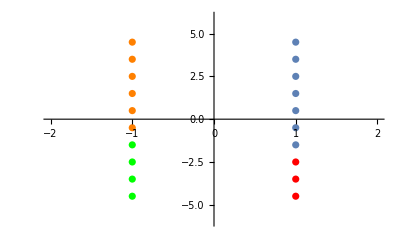

```mathematica
t1=3;
t2=4;
contour1=ListPlot[Table[{1,(i-1/2)L/n-L/2},{i,t1+1,n}],PlotRange->{{-2,2},{-6,6}}];
contour2=ListPlot[Table[{1,(i-1/2)L/n-L/2},{i,1,t1}],PlotStyle->Red];
contour3=ListPlot[Table[{-1,(i-1/2)L/n-L/2},{i,t2+1,n}],PlotRange->{-6,6},PlotStyle->Orange];
contour4=ListPlot[Table[{-1,(i-1/2)L/n-L/2},{i,1,t2}],PlotStyle->Green];
Show[contour1,contour2,contour3,contour4]
```

```mathematica
WapproxHoriz[y_,rot_,rr_]:=Dot@@Table[W2[Arot[y+rot.{(i-1/2)rr/n-rr/2,0,0,L/2}]],{i,1,n}]
```

```mathematica
Horiz[y_,rot_,rr_]:=Det[IdentityMatrix[2]-Abs[WapproxHoriz[y,rot,rr]]]
```

```mathematica
(* trying to see the error by omitting the horizontal segements *)
```

```mathematica
FindMinimum[Horiz[{y,0,0,0},IdentityMatrix[4],2],{y,-2.5}]
FindMinimum[Horiz[{y,0,0,0},{{Cos[θ],0,0,Sin[θ]},
{0,1,0,0},
{0,0,1,0},
{-Sin[θ],0,0,Cos[θ]}},2],{{y,-2.5},{θ,0}}]
```

{-0.0255814,{y→-1.69168}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.5,{y→-2.9771,θ→2.06806}}

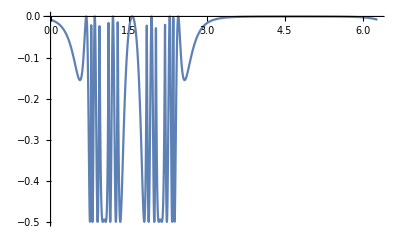

```mathematica
Plot[Horiz[{-3.55,0,0,0},{{Cos[θ],0,0,Sin[θ]},
{0,1,0,0},
{0,0,1,0},
{-Sin[θ],0,0,Cos[θ]}},2],{θ,0,2Pi},PlotRange->All]
```

```mathematica
WapproxHoriz[{-3,0,0,0},{{Cos[2.06],0,0,Sin[2.06]},
{0,1,0,0},
{0,0,1,0},
{-Sin[2.06],0,0,Cos[2.06]}},2]
```

{{-0.521677+0. ⅈ,0.+0.853143 ⅈ},{0.+0.853143 ⅈ,-0.521677+0. ⅈ}}

```mathematica
Imes[y_,rot_,rr_]:=1-1/2*Tr[Wapprox[y+rot.{rr/2,0,0,0},rot].Wdapprox[y-rot.{rr/2,0,0,0},rot]](* integrand *)
```

```mathematica
(*Obtaining random spherically distributed points.*)
RandSphere:=Module[{r,poi},r=2;
While[r>1,
poi=RandomReal[{-1,1},4];
r=Norm[poi]]; 
poi=poi/r;
poi ]
{RandSphere,RandSphere}
(*ListPlot[Table[randSphere,100],AspectRatio->1]*)
```

{{0.303666,0.5073,0.802457,0.0806025},{-0.671736,0.117196,-0.309693,0.662666}}

```mathematica
(*Random sampling of rotation matricies*)
RotR[a_]:=
{{a[[1]],-a[[2]],-a[[3]],-a[[4]]},
{a[[2]],a[[1]],-a[[4]],a[[3]]},
{a[[3]],a[[4]],a[[1]],-a[[2]]},
{a[[4]],-a[[3]],a[[2]],a[[1]]}};
RotL[p_]:={{p[[1]],-p[[2]],-p[[4]],-p[[3]]},
{p[[2]],p[[1]],p[[3]],-p[[4]]},
{p[[4]],-p[[3]],p[[1]],p[[2]]},
{p[[3]],p[[4]],-p[[2]],p[[1]]}};
Rot[a_,p_]:=RotL[a].RotR[p]
RandRot:=Rot[RandSphere,RandSphere]
```

```mathematica
RandY:=Append[RandomReal[{-l,l},3],0]
```

```mathematica
(*0.05-0.1 for rotating the lines*)
(*Similar range for rotating the fields*)
Timing[Imes[RandY,RandRot,5]]
```

{0.046875,0.00412101+0. ⅈ}

```mathematica
(*Number of test points for monte carlo*)
num=1000;
l=3;
```

```mathematica
(*Random numbers for all future points
11 is the number of distances r not related to 
points along the lines
*)
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
randRot2=Table[RandRot,11,num];
randY2=Table[RandY,11,num];
```

```mathematica
(*Unit conversion to GeV and multiplication by instanton density 12/2*)
units=43.7; (* here MeV *)
(*Conversion from ρ to GeV^-1*)
unitsr=1.4;
```

```mathematica
(* main summator 
arguments are random y and random Y *)
```

```mathematica
DistanceDataMes[rY_,rR_]:=Table[{rr,units*8l^3/num*Sum[Imes[rY[[rr/0.5+1,i]],rR[[rr/0.5+1,i]],rr/unitsr],{i,1,num}]},{rr,0,5,0.5}]
```

```mathematica
data1=DistanceDataMes[randY,randRot]
(* here particular random values from the table are put in *)
```

{{0.,34.0419+0. ⅈ},{0.5,83.2129+0. ⅈ},{1.,204.976+0. ⅈ},{1.5,308.952+0. ⅈ},{2.,427.249+0. ⅈ},{2.5,483.4+0. ⅈ},{3.,511.09+0. ⅈ},{3.5,551.108+0. ⅈ},{4.,586.201+0. ⅈ},{4.5,601.876+0. ⅈ},{5.,625.588+0. ⅈ}}

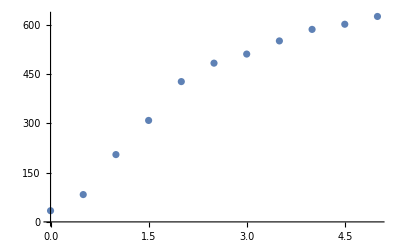

```mathematica
PlotMesMC=ListPlot[data1]
```

```mathematica
data2=DistanceDataMes[randY2,randRot2]
```

{{0.,3.55449+0. ⅈ},{0.5,34.4615+0. ⅈ},{1.,200.284+0. ⅈ},{1.5,260.314+0. ⅈ},{2.,104.854+0. ⅈ},{2.5,179.706+0. ⅈ},{3.,249.798+0. ⅈ},{3.5,1100.97+0. ⅈ},{4.,633.118+0. ⅈ},{4.5,619.847+0. ⅈ},{5.,792.63+0. ⅈ}}

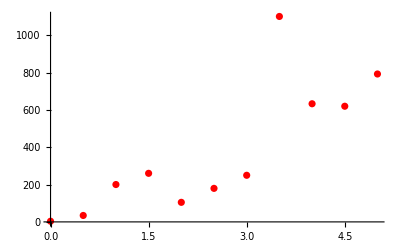

```mathematica
PlotMesMC2=ListPlot[data2, PlotStyle->Red]
```

```mathematica
Show[PlotMesMC,PlotMesMC2]
```

Show::gcomb: Could not combine the graphics objects in Show[,PlotMesMC2].

Show[-Graphics-,PlotMesMC2]

```mathematica
(*Field Strength*)
Fmunu=Table[D[Arot[{y[1],y[2],y[3],y[4]}][[mu]][[a]],y[nu] ]-D[Arot[{y[1],y[2],y[3],y[4]}][[nu]][[a]],y[mu] ],{mu,1,4},{nu,1,4},{a,1,3}]+Table[
-Sum[
LeviCivitaTensor[3][[a,b,c]]Arot[{y[1],y[2],y[3],0}][[mu]][[b]]Arot[{y[1],y[2],y[3],0}][[nu]][[c]],{b,1,3},{c,1,3}],
{mu,1,4},{nu,1,4},{a,1,3}];
Dimensions[Fmunu]
```

{4,4,3}

```mathematica
B[yy_]:=Table[1/2Sum[LeviCivitaTensor[3][[i]][[j]][[k]](Fmunu[[j,k,a]]/.{y[1]->yy[[1]],y[2]->yy[[2]],y[3]->yy[[3]],y[4]->yy[[4]]})PauliMatrix[a] ,{j,1,3},{k,1,3},{a,1,3}],{i,1,3}]
Ee[yy_]:=Table[1/2Sum[(Fmunu[[4,i,a]]/.{y[1]->yy[[1]],y[2]->yy[[2]],y[3]->yy[[3]],y[4]->yy[[4]]})PauliMatrix[a] ,{a,1,3}],{i,1,3}]
```

```mathematica
B[RandY][[1]]
Ee[RandY][[1]]
```

{{-0.0116807,-0.073509-0.0521642 ⅈ},{-0.073509+0.0521642 ⅈ,0.0116807}}

{{0.,0.+0. ⅈ},{0.+0. ⅈ,0.}}

```mathematica
(*Integrand for two B fields*)
ImesBB[y_,rot_,rr_,t1_,t2_]:=Sum[Tr[WApproxLower[y+rot.{rr/2,0,0,0},rot,t1].B[y+rot.{rr/2,0,0,0}+rot.{0,0,0,t1}][[i]].WApproxUpper[y+rot.{rr/2,0,0,0},rot,t1].WdApproxUpper[y-rot.{rr/2,0,0,0},rot,t2].B[y-rot.{rr/2,0,0,0}+rot.{0,0,0,t2}][[i]].WdApproxLower[y-rot.{rr/2,0,0,0},rot,t2]],{i,1,3}]
```

```mathematica
AbsoluteTiming[Sum[ImesBB[RandY,RandRot,3,t1,t2](L/n)^2,{t1,1,n},{t2,1,n}]]
```

{25.9554,0.0517092+0. ⅈ}

```mathematica
num=100;
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
```

```mathematica
DistanceDataMesBB[rY_,rR_]:=Table[{rr,units*8l^3/num*Sum[Sum[ImesBB[rY[[rr/0.5+1,i]],rR[[rr/0.5+1,i]],rr/unitsr,t1,t2](L/n)^2,{t1,1,n},{t2,1,n}],{i,1,num}]},{rr,0,5,0.5}]
```

```mathematica
data1BB=DistanceDataMesBB[randY,randRot]
```

{{0.,27301.7+0. ⅈ},{0.5,8054.15+0. ⅈ},{1.,1376.66+0. ⅈ},{1.5,1504.33+0. ⅈ},{2.,462.679+0. ⅈ},{2.5,140.77+0. ⅈ},{3.,439.736+0. ⅈ},{3.5,-7.15806+0. ⅈ},{4.,153.611+0. ⅈ},{4.5,-200.154+0. ⅈ},{5.,-65.2629+0. ⅈ}}

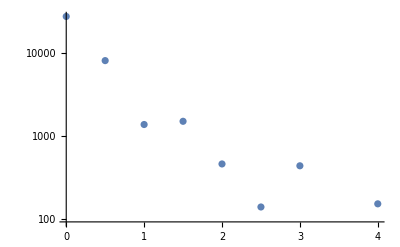

```mathematica
ListLogPlot[data1BB]
```

```mathematica
(*SU(3) matrix for baryon*)
Wapprox3[y_,rot_]:=SparseArray[ArrayFlatten[{{Wapprox[y,rot],0},{0,1}}]]
```

```mathematica
(*Baryon Integrand-Direct Triangle*)
Ibar[y_,rot_,rr_]:=1+1/6(LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[1]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[2]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[3]]+
LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[3]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[1]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[2]]+LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[2]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[3]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[1]]-
LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[1]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[3]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[2]]-
LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[2]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[1]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[3]]-LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[3]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[2]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[1]])
```

```mathematica
Timing[Ibar[{100,0,0,0},RandRot,5]]
```

{0.359375,2.5287×10^-8+5.29396×10^-23 ⅈ}

```mathematica
num=1000;
l=7;
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
```

```mathematica
DistanceDataBar=Table[{rr,units*8l^3/num*Sum[Ibar[randY[[rr/0.5+1,i]],randRot[[rr/0.5+1,i]],rr/(2unitsr)],{i,1,num}]},{rr,0,5,0.5}]
```

{{0.,8.0943×10^-12+0. ⅈ},{0.5,91.3833+9.55593×10^-16 ⅈ},{1.,113.216+2.5923×10^-16 ⅈ},{1.5,151.197+1.77866×10^-16 ⅈ},{2.,87.869-5.20394×10^-16 ⅈ},{2.5,384.238-4.02704×10^-16 ⅈ},{3.,468.207+4.36481×10^-16 ⅈ},{3.5,467.523-3.0072×10^-15 ⅈ},{4.,344.26+3.76063×10^-16 ⅈ},{4.5,748.778-5.06835×10^-16 ⅈ},{5.,868.616-2.28406×10^-16 ⅈ}}

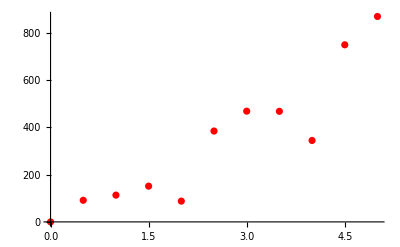

```mathematica
PlotBar=ListPlot[DistanceDataBar,PlotStyle->Red]
```

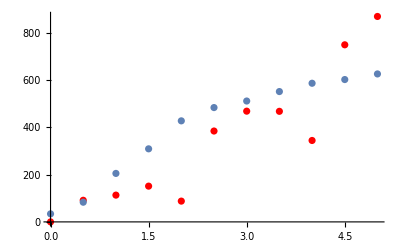

```mathematica
Show[PlotBar, PlotMesMC]
```

```mathematica
Wdapprox3[y_,rot_]:=SparseArray[ArrayFlatten[{{Wapprox[y,rot],0},{0,1}}]]
```

```mathematica
TetraStructure[wd1_,wd2_,wd3_,wd4_]=Permute[{wd1,wd2,wd3,wd4},SymmetricGroup[4]]
```

{{wd1,wd2,wd3,wd4},{wd1,wd2,wd4,wd3},{wd1,wd3,wd2,wd4},{wd1,wd3,wd4,wd2},{wd1,wd4,wd2,wd3},{wd1,wd4,wd3,wd2},{wd2,wd1,wd3,wd4},{wd2,wd1,wd4,wd3},{wd2,wd3,wd1,wd4},{wd2,wd3,wd4,wd1},{wd2,wd4,wd1,wd3},{wd2,wd4,wd3,wd1},{wd3,wd1,wd2,wd4},{wd3,wd1,wd4,wd2},{wd3,wd2,wd1,wd4},{wd3,wd2,wd4,wd1},{wd3,wd4,wd1,wd2},{wd3,wd4,wd2,wd1},{wd4,wd1,wd2,wd3},{wd4,wd1,wd3,wd2},{wd4,wd2,wd1,wd3},{wd4,wd2,wd3,wd1},{wd4,wd3,wd1,wd2},{wd4,wd3,wd2,wd1}}

```mathematica
Wdvars[y_,rot_,rr_]:={Wdapprox3[y,rot],Wdapprox3[y+{rr,0,0,0},rot],Wdapprox3[y+{0,rr,0,0},rot],Wdapprox3[y+{0,0,rr,0},rot]}
```

```mathematica
(TetraStructure@@(Wdvars[RandY,RandRot,5]))[[1,1]]
```

SparseArray[…]

```mathematica
Itetra[y_,rot_,rr_]:=1-1/(24*3^4)*Sum[Tr[Wapprox3[y,rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,1]]]Tr[Wapprox3[y+{rr,0,0,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,2]]]Tr[Wapprox3[y+{0,rr,0,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,3]]]Tr[Wapprox3[y+{0,0,rr,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,4]]],{i,1,24}]
```

```mathematica
AbsoluteTiming[Itetra[0,RandRot,0]]
```

{24.0004,0.238155+0. ⅈ}

```mathematica
num=100
```

100

```mathematica
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
```

```mathematica
8l^3/num*Sum[Itetra[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
8l^3/num*Sum[Itetra[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];8l^3/num*Sum[Itetra[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
```

285.178+1.64404×10^-16 ⅈ

380.19+4.34851×10^-16 ⅈ

313.398-2.5268×10^-16 ⅈ

```mathematica
DistanceDataTetra=Table[{rr,l^3/num*Sum[Itetra[randY[[rr/2+1,i]],randRot[[rr/2+1,i]],rr],{i,1,num}]},{rr,0,20,2}]
```

{{0,221.942+0. ⅈ},{2,287.467-6.36019×10^-17 ⅈ},{4,324.485-3.84447×10^-17 ⅈ},{6,274.969-2.97889×10^-17 ⅈ},{8,189.001-1.90213×10^-16 ⅈ},{10,235.61-2.42636×10^-16 ⅈ},{12,289.236-3.05355×10^-16 ⅈ},{14,178.536-8.24822×10^-16 ⅈ},{16,203.514-1.40206×10^-16 ⅈ},{18,135.131-8.64395×10^-17 ⅈ},{20,96.4279-1.06337×10^-16 ⅈ}}

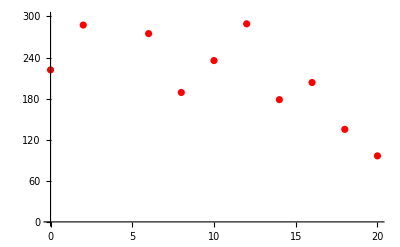

```mathematica
PlotTetra=ListPlot[Re[DistanceDataTetra],PlotRange->{0,300},PlotStyle->Red]
```